## Importing Data

```mathematica
SetDirectory["/Users/kevin/SkyDrive/Modern Physics Lab Atomic Nucleus"];
```

```mathematica
alum = FileNames["*Aluminum.lst"];
plas = FileNames["*plastic.lst"];
```

```mathematica
plas
```

{Cs137_1plastic.lst,Cs137_2plastic.lst,Cs137_3plastic.lst,Cs137_4plastic.lst,Cs137_5plastic.lst,Cs137_7plastic.lst}

```mathematica
junk={alum,plas};
```

```mathematica
lengthAlumList=Table[x,{x,1,First[alum//Dimensions]}];
```

```mathematica
lengthPlasList=Table[x,{x,1,First[plas//Dimensions]}];
```

## Organize Data

```mathematica
alumData=Map[ImportString[StringReplace[Import[alum[[#]],"Text"],{"          "->","}],"csv"]&,lengthAlumList];
```

```mathematica
plasData=Map[ImportString[StringReplace[Import[plas[[#]],"Text"],{"          "->","}],"csv"]&,lengthPlasList];
```

```mathematica
Export["alumData2.mat",alumData[[All,{{1},{9;;}}]]]
```

alumData2.mat

```mathematica
Export["plasData.mat",plasData[[All,9;;]]]
```

plasData.mat

```mathematica
alumData[[1,{1,2}|{2,4}]]
```

{{{$SPEC_ID:},{ACQUISITION_1},{$DATE_MEA:},«8194»,{8189,0},{8190,0},{8191,0}},«4»,{{$SPEC_ID:},«8199»}}⟦1,«1»⟧

```mathematica
alumData[[1,{1,2,3,5}]]
```

{{$SPEC_ID:},{ACQUISITION_1},{$DATE_MEA:},{$MEAS_TIM:}}

## Plot Initial Data

```mathematica
plasData[[1,9;;2000,2]];
```

{0,0,0,0,0,0,0,0,2,0,0,0,0,1,2,2,0,2,0,4,6,5,10,12,10,10,27,17,40,47,58,87,104,137,137,120,164,143,155,170,161,139,166,177,182,133,177,181,161,166,150,163,173,159,159,181,168,170,168,173,156,169,177,180,151,172,174,174,175,175,171,193,179,178,171,167,157,171,163,153,186,175,146,148,182,173,165,144,147,134,143,144,162,171,153,170,148,135,144,142,157,179,127,131,159,177,158,141,156,144,149,141,145,146,153,129,151,126,157,133,157,155,141,145,173,156,139,169,140,146,134,146,164,149,160,144,136,148,141,150,139,145,154,157,160,161,138,143,141,144,149,153,157,138,163,141,165,164,143,156,140,158,151,136,138,177,156,158,145,184,179,161,155,151,155,135,158,152,138,152,146,173,170,159,174,172,167,155,168,166,170,151,183,177,149,171,145,183,178,178,167,184,170,149,144,149,180,171,169,169,195,189,157,154,187,143,158,159,184,164,166,168,179,168,162,182,195,173,171,178,158,149,180,182,205,179,165,175,169,188,185,141,167,197,156,188,165,176,169,174,171,176,213,161,168,187,156,191,165,169,188,180,177,188,185,182,189,176,187,191,170,192,196,190,167,175,160,155,193,172,170,176,191,179,182,188,181,194,168,198,191,187,177,193,172,179,182,190,165,165,186,169,201,188,208,173,185,191,153,167,177,191,205,172,208,190,182,188,202,172,193,180,152,184,182,188,191,192,194,174,185,169,179,175,182,174,166,184,184,176,177,176,204,178,183,171,172,188,180,165,181,181,187,190,179,182,192,205,210,166,178,171,181,171,184,173,176,200,191,207,193,215,199,180,187,169,174,192,174,163,178,189,198,204,162,172,192,176,172,177,211,172,185,202,181,182,172,169,168,186,175,206,190,187,176,170,222,153,190,212,176,214,164,174,171,172,185,163,169,142,171,168,200,167,173,187,170,193,185,176,175,173,187,177,180,174,173,166,173,183,180,217,188,185,204,187,187,205,174,192,162,182,188,196,170,181,145,183,182,191,157,159,163,172,212,167,164,196,212,188,157,161,178,175,206,188,163,177,155,164,173,209,174,181,155,181,181,190,185,189,195,208,178,175,193,184,187,176,205,183,188,176,202,203,182,217,171,169,181,173,210,168,166,187,161,179,191,164,177,173,168,181,187,161,202,171,170,184,158,177,167,149,179,184,181,177,167,182,206,180,188,171,177,169,161,163,158,173,190,158,171,174,160,192,178,195,188,196,184,149,157,194,187,155,150,168,157,158,168,175,151,151,181,158,171,174,177,166,175,148,156,164,184,165,181,176,175,171,183,168,169,183,166,163,176,169,166,156,164,160,180,180,154,163,151,174,161,155,149,148,151,156,158,180,183,173,165,193,158,171,144,173,158,169,162,172,176,184,170,162,167,173,174,136,136,162,168,160,152,155,161,160,153,176,176,164,190,141,160,146,175,153,179,158,165,155,171,155,149,162,189,154,138,156,148,160,150,169,158,162,150,171,153,144,170,138,157,157,169,151,151,157,149,142,150,151,150,161,129,163,145,168,145,170,138,125,166,161,175,145,147,142,146,158,152,164,154,147,164,157,140,141,150,162,177,130,170,157,132,163,137,125,146,147,152,167,132,137,156,128,131,136,126,142,143,144,157,133,154,137,135,130,130,109,152,141,115,149,145,149,134,141,135,135,148,126,147,133,121,157,137,164,154,130,127,133,124,142,162,151,114,115,153,139,122,131,142,150,116,155,148,121,154,134,137,146,127,142,132,138,119,139,123,134,128,126,131,129,149,126,116,126,127,122,114,131,134,134,144,147,122,130,127,123,134,126,128,126,142,113,106,118,114,122,133,119,139,122,108,125,113,96,105,149,109,99,116,139,133,141,118,102,125,128,132,129,107,122,128,110,104,123,111,122,104,108,120,127,122,129,121,127,108,113,110,110,118,117,122,104,141,97,120,104,118,123,124,121,114,119,118,118,96,108,118,121,120,105,99,105,119,110,127,119,91,112,116,105,138,104,97,94,100,108,95,125,100,128,101,84,91,117,92,108,112,109,106,90,108,108,102,104,97,103,121,127,82,86,101,96,107,94,87,93,109,99,104,112,102,103,100,98,101,75,111,101,92,105,97,99,102,107,116,118,124,96,103,99,101,105,106,93,105,94,97,106,100,90,99,99,92,101,97,92,90,79,100,87,96,83,69,82,69,92,85,83,93,97,81,103,96,88,84,84,104,87,87,99,99,84,88,89,99,99,72,77,55,97,87,78,75,62,76,90,93,80,92,73,73,86,78,90,75,79,77,86,83,96,77,79,85,98,75,71,87,88,67,91,86,66,75,72,85,80,80,80,73,73,90,78,75,63,83,74,70,82,75,81,90,60,71,79,67,85,63,77,81,70,77,69,59,80,72,88,67,68,73,73,71,78,83,69,72,49,71,76,69,67,81,69,91,75,63,59,60,68,65,71,76,68,62,75,68,68,68,72,69,58,71,78,78,67,65,67,76,66,75,74,68,57,59,87,61,69,76,54,64,59,64,61,71,65,58,64,58,64,70,64,66,47,56,55,52,63,52,69,62,75,62,67,61,64,69,61,90,58,73,55,60,59,65,42,64,64,68,46,71,57,62,69,57,58,48,59,59,56,66,54,64,74,65,75,49,53,58,58,58,53,57,48,51,46,47,51,66,62,61,51,54,44,67,47,57,62,57,47,39,49,50,56,46,50,56,50,50,68,49,47,54,53,48,57,35,51,60,49,54,58,52,41,49,37,48,55,57,58,51,56,36,51,51,36,65,69,62,44,48,54,52,47,51,45,49,47,42,50,40,61,56,42,41,43,48,48,41,42,49,51,47,41,43,49,44,50,49,35,44,48,36,39,39,39,49,46,46,48,55,51,35,36,46,39,47,53,56,44,41,46,37,34,50,46,46,32,35,43,36,43,53,45,44,36,40,46,40,44,31,41,53,40,38,29,29,33,47,34,47,29,37,41,46,39,42,43,51,36,33,39,31,29,36,38,36,39,40,42,45,37,40,37,31,42,35,46,27,34,37,41,35,38,45,52,38,28,37,42,40,33,35,39,47,32,37,38,50,27,33,31,28,32,38,47,43,49,31,38,36,28,26,41,32,34,42,40,28,31,36,36,40,36,29,42,36,45,37,33,36,34,33,31,25,36,39,32,31,29,31,35,24,41,39,35,34,30,30,43,24,33,28,38,42,33,43,43,25,46,26,41,29,29,34,45,38,30,35,33,42,26,33,28,27,38,32,31,37,38,35,35,29,30,32,32,36,36,34,31,33,34,47,37,28,31,22,24,24,30,28,32,38,25,21,31,33,26,26,25,29,20,33,29,30,30,33,31,35,41,21,30,36,34,39,33,37,40,22,27,27,28,28,31,35,32,33,45,26,29,30,26,37,33,28,33,27,30,35,31,33,32,27,38,40,30,30,29,40,39,41,30,32,30,27,27,37,27,31,34,30,23,33,27,31,34,42,29,44,29,30,32,32,30,44,37,41,34,32,21,28,38,37,33,37,34,44,35,40,33,37,33,39,36,36,35,47,41,46,40,49,29,40,32,39,40,39,37,36,53,35,44,31,37,34,46,38,43,41,47,42,39,31,42,34,46,45,43,50,45,36,43,44,39,35,57,52,41,27,47,51,53,40,41,54,35,52,36,41,50,52,39,52,40,38,55,47,41,43,53,56,49,42,64,42,40,44,53,37,47,41,60,47,32,38,56,65,47,49,51,50,56,60,36,63,44,51,57,38,54,54,60,59,56,54,56,65,62,64,57,57,61,46,70,63,68,70,60,57,72,65,51,58,57,53,62,64,49,60,49,72,64,66,58,57,43,70,66,68,61,64,58,77,66,59,74,57,61,77,67,69,58,85,65,68,58,54,55,64,51,58,66,79,67,58,58,73,54,58,54,64,75,57,73,74,72,72,64,80,52,76,78,76,76,71,77,66,81,76,67,62,87,74,72,66,74,64,71,82,76,80,59,76,81,71,63,67,70,63,59,72,65,77,54,66,81,65,72,61,68,86,73,85,59,56,74,60,69,70,66,65,75,73,80,69,65,72,60,63,66,69,74,56,62,58,74,57,65,64,68,57,55,74,66,76,57,58,82,61,63,79,55,57,52,59,58,48,54,55,73,53,62,64,44,55,53,60,45,50,53,47,63,51,52,57,58,56,43,62,46,65,40,56,53,53,48,58,64,54,43,50,50,39,43,39,62,45,58,46,50,52,48,50,60,54,32,38,44,45,61,54,37,46,34,42,42,37,54,42,39,39,39,39,41,31,31,42,39,33,40,36,29,36,36,27,22,33,29,27,25,34,27,19,30,31,30,34,25,37,29,28,40,27,24,27,27,28,27,18,30,29,22,18,20,13,21,12,29,18,32,23,22,20,10,17,22,14,17,11,23,21,11,18,19,23,13,24,19,14,17,18,17,15,16,26,13,18,15,12,23,16,6,16,17,12,16}

```mathematica
f=ListInterpolation[plasData[[1,9;;2000,2]]]
```

InterpolatingFunction[{{1,1992}},<>]

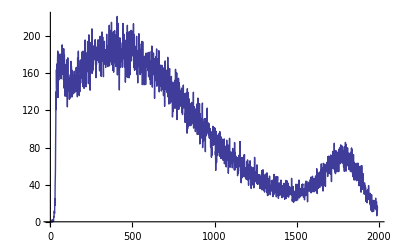

```mathematica
interpPlot=Plot[f[x],{x,1,1992}]
```

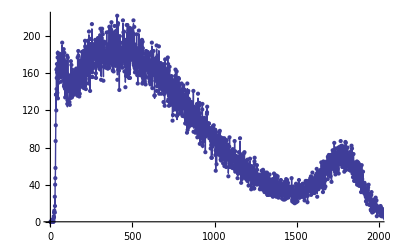

```mathematica
Show[interpPlot,ListPlot[plasData[[1,9;;4900,2]]]]
```

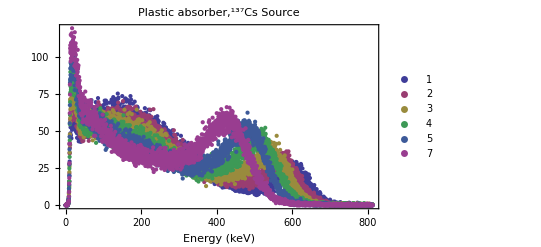

```mathematica
plasticShifts=ListPlot[plasData[[1;;,9;;2400]] 624.259/1838,PlotRange->All,PlotLegends->{"1","2","3","4","5","7"},Frame->True,PlotLabel->"Plastic absorber,^137Cs Source",FrameLabel->{"Energy (keV)",""}]
```

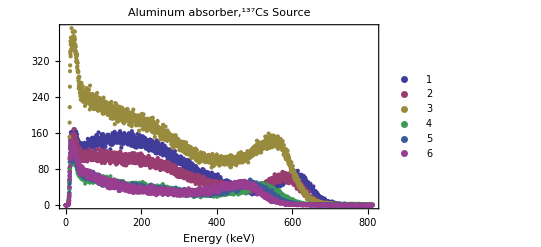

```mathematica
aluminumShifts=ListPlot[alumData[[1;;,9;;2400]] 624.259/1838,PlotRange->All,PlotLegends->{"1","2","3","4","5","6"},Frame->True,PlotLabel->"Aluminum absorber,^137Cs Source",FrameLabel->{"Energy (keV)",""}]
```

```mathematica
SetDirectory["/Users/kevin/SkyDrive/KTH Work/LaTeX Reports/Atomic Nucleus/Figures"];
```

```mathematica
Export["aluminumShiftsPlot.eps",aluminumShifts]
```

aluminumShiftsPlot.eps

```mathematica
Export["plasticShiftsPlot.eps",plasticShifts]
```

plasticShiftsPlot.eps